### Standard 2D Definitions:

```mathematica
getCoefficient[f_,x_,l_Integer]:=If[l==-1,f[0],If[l==0,f[1]-f[0],f[x]-1/2. f[x+2^-l]-1/2. f[x-2^-l]]]

getCoefficient2D[f_,x_,y_,lx_,ly_]:=getCoefficient[Function[y1,getCoefficient[Function[x1,f[x1,y1]],x,lx]],y,ly]
(* Tensor product construction
*)

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^switch[kx]-1,2},{j,1,2^switch[ky]-1,2}],{kx,-1,lx},{ky,-1,ly}]


Reconstruct2D[coefficients_]:= Sum[coefficients[[kx+2,ky+2,ceil[#1,switch[kx]],ceil[#2,switch[ky]]]] 
ϕ[kx,ky,ceil[#1,switch[kx]],ceil[#2,switch[ky]]][#1,#2]
,{kx,-1,Length[coefficients]-2},{ky,-1,Length[coefficients]-2}]&
```

```mathematica
neighborAverage1D[f_,x_List,n_]:=Module[{below,above},below=2^-n Floor[x[[1]] 2^n];above=2^-n Ceiling[x[[1]] 2^n]; If[above==below,Return[f[{above}]];,Return[(above-x[[1]])/(above-below)f[{below}]+(x[[1]]-below)/(above-below)f[{above}]];]]

neighborAverage[f_,x_,n_]:=Module[{above,below},If[Length[x]==1,Return[neighborAverage1D[f,x,n]];,
Return[neighborAverage1D[Function[q,neighborAverage[Function[p,f[Join[q,p]]],x[[2;;]],n]],{x[[1]]},n]
] (*A little convoluted, but still efficient*)
]
]
```

```mathematica
Plot3D[neighborAverage[Sin[Pi #[[1]]+#[[2]]]&,{x,y},3]-fullReconstruct[#,{x,y},{3,3}],{x,0,1},{y,0,1}]&@fullCoefficients[Sin[Pi #[[1]]+#[[2]]]&,{3,3}] (*Good*)
```

-Graphics3D-

```mathematica
neighborError2D[f_,n_,stepsize_]:=Module[{ans},ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-neighborAverage[f,{i,j},n])^2,{i,0,1,stepsize},{j,0,1,stepsize}]]; Return[ans]]

neighborError3D[f_,n_,stepsize_]:=Module[{ans},ans=Sqrt[stepsize^2 Sum[(f[{i,j,k}]-neighborAverage[f,{i,j,k},n])^2,{i,0,1,stepsize},{j,0,1,stepsize},{k,0,1,stepsize}]]; Return[ans]]

sparseNeighborError2D[f_,n_,stepsize_]:=Module[{values,ans,i,j,coeffs},coeffs=sparseCoefficients[f,n,2];
For[i=0,i≤1,i+=2^-n,For[j=0,j≤1,j+=2^-n,
f[{i,j}]=sparseReconstruct[]]]
ans=Sqrt[stepsize^2 Sum[(f[{i,j}]-neighborAverage[values,{i,j},n])^2,{i,0,1,stepsize},{j,0,1,stepsize}]]; Return[ans]]
```

```mathematica
timesAndErrors2D=Table[neighborError2D[Sin[Pi #[[1]]+#[[2]]]&,n,.005]//Timing,{n,1,9}];
```

```mathematica
timesAndErrors3D=Table[Timing[neighborError3D[Sin[Pi #[[1]]+#[[2]]+#[[3]]]&,n,.05]],{n,1,9}]
```

{{2.74913,0.797945},{2.53602,0.211164},{2.68177,0.0536385},{2.76519,0.0134631},{2.79475,0.00336914},{2.80355,0.000842495},{2.80076,0.000210637},{2.8397,0.00005266},{2.83865,0.000013165}}

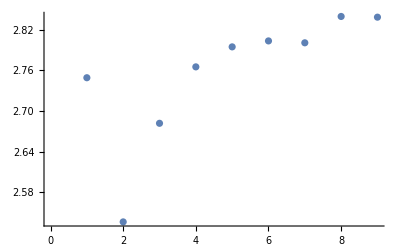

```mathematica
ListPlot[timesAndErrors3D[[;;,1]]]
```

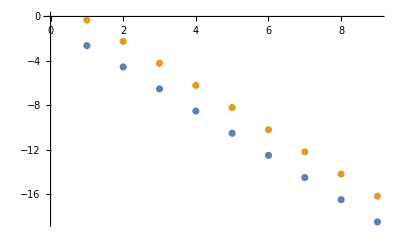

```mathematica
ListPlot[{timesAndErrors2D[[;;,2]],timesAndErrors3D[[;;,2]]}//Log2]
```

```mathematica
Table[neighborError2D[Sin[Pi #[[1]]+#[[2]]]&,n,.01]//Timing,{n,1,9}]
```

{{1.40354,0.161664},{1.47964,0.0426418},{1.57263,0.0108044},{1.61937,0.00271017},{1.65168,0.000678109},{1.68744,0.000169563},{1.70248,0.0000423929},{1.69213,0.0000105984},{1.69154,2.6496×10^-6}}

```mathematica
Table[neighborError2D[Sin[Pi #[[1]]+#[[2]]]&,n,.05]//Timing,{n,1,9}]
```

{{0.060661,0.164283},{0.061467,0.0431182},{0.062476,0.0109221},{0.062417,0.00273951},{0.064861,0.000685441},{0.061684,0.000171395},{0.063721,0.0000428511},{0.064688,0.0000107129},{0.063336,2.67823×10^-6}}

```mathematica
test2D[x_,y_]:=Sin[Pi x + y]

Table[Sqrt[(.01)^2 Sum[(test2D[x,y]-#[x,y])^2,{x,0,1,.01},{y,0,1,.01}]&@project2D[test2D,n,n]]//N,{n,1,6}]
```

{2.37074,2.44771,2.46918,2.4747,2.47609,2.47644}

```mathematica
fullError2D={0.1616637516206237,0.04264183600024855,0.01080439368393583,0.0027101651375167715,0.0006781090641505266,0.00016956276998884528};
```

```mathematica
error20Points={{0.058794,0.16428309358579668},{0.054117,0.04311824666968757},{0.056035,0.010922142274398583},{0.061692,0.00273951470709909},{0.059793,0.0006854411527070644},{0.064058,0.00017139537512743638},{0.061762,0.00004285105877639942},{0.06311,0.000010712898230790916},{0.061615,2.678234120154341*^-6}};
```

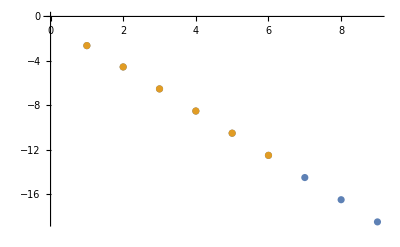

```mathematica
Show[ListPlot[{timesAndErrors[[;;,2]],fullError2D}//Log2]]
```